```mathematica
e1=-h (x1-0.5) (-0.5)-h (x2-0.5) (-0.5);
e2=-h (x1-0.5) (1-0.5)-h (x2-0.5) (-0.5);
e3=-h (x1-0.5) (-0.5)-h (x2-0.5) (1-0.5);
e4=-h (x1-0.5) (1-0.5)-h (x2-0.5) (1-0.5)+0.5 γ(-1)^2;
e5=-h (x1-0.5) (-0.5)-h (x2-0.5) (-0.5)+0.5 γ(1)^2;
e6=-h (x1-0.5) (1-0.5)-h (x2-0.5) (-0.5)+0.5 γ(1)^2;
e7=-h (x1-0.5) (-0.5)-h (x2-0.5) (1-0.5)+0.5 γ(1)^2;
e8=-h (x1-0.5) (1-0.5)-h (x2-0.5) (1-0.5);
```

```mathematica
ee1=-h (x1-0.5) (-0.5)-h (x2-0.5) (-0.5);
ee2=-h (x1-0.5) (1-0.5)-h (x2-0.5) (-0.5);
ee3=-h (x1-0.5) (-0.5)-h (x2-0.5) (1-0.5);
ee4=-h (x1-0.5) (1-0.5)-h (x2-0.5) (1-0.5);
ee5=-h (x1-0.5) (-0.5)-h (x2-0.5) (-0.5);
ee6=-h (x1-0.5) (1-0.5)-h (x2-0.5) (-0.5);
ee7=-h (x1-0.5) (-0.5)-h (x2-0.5) (1-0.5);
ee8=-h (x1-0.5) (1-0.5)-h (x2-0.5) (1-0.5);
```

```mathematica
W={{0,Exp[e2],Exp[e3],0,Exp[e5],0,0,0},
{Exp[e1],0,0,Exp[e4],0,Exp[e6],0,0},
{Exp[e1],0,0,Exp[e4],0,0,Exp[e7],0},
{0,Exp[e2],Exp[e3],0,0,0,0,Exp[e8]},
{Exp[e1],0,0,0,0,Exp[e6],Exp[e7],0},
{0,Exp[e2],0,0,Exp[e5],0,0,Exp[e8]},
{0,0,Exp[e3],0,Exp[e5],Exp[e6],0,0},
{0,0,0,Exp[e4],0,Exp[e6],Exp[e7],0}};
```

```mathematica
Wneq={{0,Exp[ee2],Exp[ee3],0,Exp[ee5+γ(1-1/2)],0,0,0},
{Exp[ee1],0,0,Exp[ee4],0,Exp[ee6+γ(1-1/2)],0,0},
{Exp[ee1],0,0,Exp[ee4],0,0,Exp[ee7+γ(1-1/2)],0},
{0,Exp[ee2],Exp[ee3],0,0,0,0,Exp[ee8+γ(-1/2)]},
{Exp[ee1+γ(-1/2)],0,0,0,0,Exp[ee6],Exp[ee7],0},
{0,Exp[ee2+γ(-1/2)],0,0,Exp[ee5],0,0,Exp[ee8]},
{0,0,Exp[ee3+γ(-1/2)],0,Exp[ee5],Exp[ee6],0,0},
{0,0,0,Exp[ee4+γ(1-1/2)],0,Exp[ee6],Exp[ee7],0}};
```

```mathematica
For[i=1,i<=8,i++,
W[[i,i]]=-Sum[W[[j,i]],{j,1,8}];
Wneq[[i,i]]=-Sum[Wneq[[j,i]],{j,1,8}];]
```

```mathematica
(W[[1,2]]W[[2,4]]W[[4,3]]W[[3,1]])/(W[[2,1]]W[[4,2]]W[[3,4]]W[[1,3]])//FullSimplify
(Wneq[[1,2]]Wneq[[2,4]]Wneq[[4,3]]Wneq[[3,1]])/(Wneq[[2,1]]Wneq[[4,2]]Wneq[[3,4]]Wneq[[1,3]])//FullSimplify
```

1.

1.

```mathematica
(W[[1,5]]W[[5,6]]W[[6,8]] W[[8,4]]W[[4,3]]W[[3,1]])/(W[[5,1]]W[[6,5]]W[[8,6]] W[[4,8]]W[[3,4]]W[[1,3]])//FullSimplify
(Wneq[[1,5]]Wneq[[5,6]]Wneq[[6,8]] Wneq[[8,4]]Wneq[[4,3]]Wneq[[3,1]])/(Wneq[[5,1]]Wneq[[6,5]]Wneq[[8,6]] Wneq[[4,8]]Wneq[[3,4]]Wneq[[1,3]])//FullSimplify
```

1.

ⅇ^(2 γ)

```mathematica
λvec=Eigenvalues[W/.h->10/.γ->30/.{x1->0,x2->0}];
evec=Eigenvectors[W/.h->10/.γ->30/.{x1->0,x2->0}];
```

```mathematica
λvecNeq=Eigenvalues[Wneq/.h->10/.γ->30/.{x1->0,x2->0}];
evecNeq=Eigenvectors[Wneq/.h->10/.γ->30/.{x1->0,x2->0}];
```

```mathematica
pss=evec[[8]]/Total[evec[[8]]];
```

```mathematica
pssNeq=evecNeq[[8]]/Total[evecNeq[[8]]];
```

```mathematica
csub1=Flatten[NSolve[Flatten[Join[{pss[[1]]+Sum[evec[[j]][[1]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,2,7}]}]],Table[c[j],{j,1,7}]]]
```

{c[1]→-7.19917×10^-18,c[2]→-1.27513×10^-12,c[3]→-3.57813×10^-12,c[4]→-1.50033×10^-7,c[5]→0.0000120071,c[6]→0.0000143954,c[7]→-0.0168442}

```mathematica
cNeq1=Flatten[NSolve[Flatten[Join[{pssNeq[[1]]+Sum[evecNeq[[j]][[1]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,2,7}]}]],Table[c[j],{j,1,7}]]]
```

{c[1]→7.59696×10^-20,c[2]→-6.4961×10^-15,c[3]→-4.59344×10^-15,c[4]→1.32337×10^-13,c[5]→-8.62221×10^-7,c[6]→0.00482908,c[7]→0.0189302}

```mathematica
csub2=Flatten[NSolve[Flatten[Join[{pss[[4]]+Sum[evec[[j]][[4]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,1,3}],Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,5,7}]}]],Table[c[j],{j,1,7}]]]
```

{c[1]→1.1547,c[2]→5.61234×10^-6,c[3]→5.93801×10^-6,c[4]→-0.000375522,c[5]→-0.391764,c[6]→0.0355914,c[7]→1.16216}

```mathematica
cNeq2=Flatten[NSolve[Flatten[Join[{pssNeq[[4]]+Sum[evecNeq[[j]][[4]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,1,3}],Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,5,7}]}]],Table[c[j],{j,1,7}]]]
```

{c[1]→1.41421,c[2]→0.0000914198,c[3]→0.0000646436,c[4]→2.95472×10^-9,c[5]→-1.40941,c[6]→-0.00482908,c[7]→-1.40481}

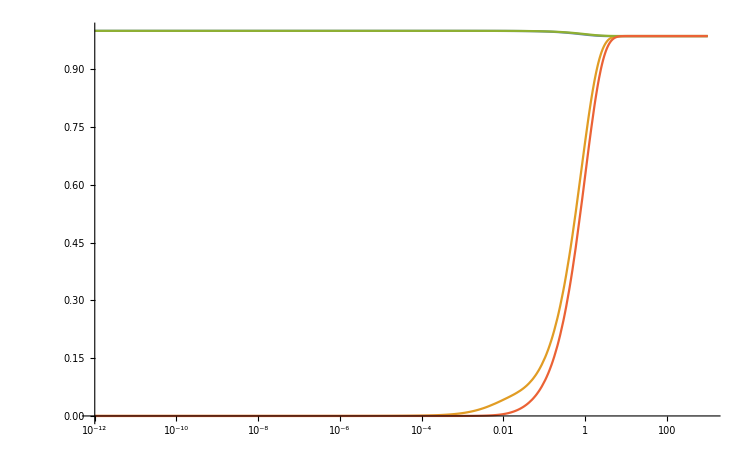

```mathematica
LogLinearPlot[{(pss[[1]]+Sum[evec[[j]][[1]] c[j]Exp[λvec[[j]] t],{j,1,7}]+pss[[5]]+Sum[evec[[j]][[5]] c[j]Exp[λvec[[j]] t],{j,1,7}])/.csub1,(pss[[1]]+Sum[evec[[j]][[1]] c[j]Exp[λvec[[j]] t],{j,1,7}]+pss[[5]]+Sum[evec[[j]][[5]] c[j]Exp[λvec[[j]] t],{j,1,7}])/.csub2,(pssNeq[[1]]+Sum[evecNeq[[j]][[1]] c[j]Exp[λvecNeq[[j]] t],{j,1,7}]+pssNeq[[5]]+Sum[evecNeq[[j]][[5]] c[j]Exp[λvecNeq[[j]] t],{j,1,7}])/.cNeq1,(pssNeq[[1]]+Sum[evecNeq[[j]][[1]] c[j]Exp[λvecNeq[[j]] t],{j,1,7}]+pssNeq[[5]]+Sum[evecNeq[[j]][[5]] c[j]Exp[λvecNeq[[j]] t],{j,1,7}])/.cNeq2},{t,10^-12,1000},PlotRange->All]
```